```mathematica
SetDirectory[NotebookDirectory[]];

gfactor=Import["g-factor","TSV"];
```

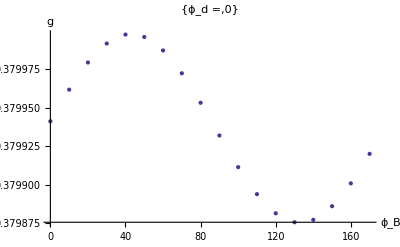
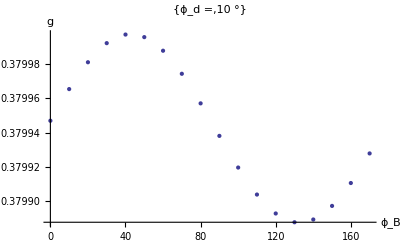
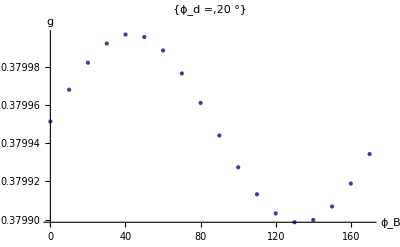
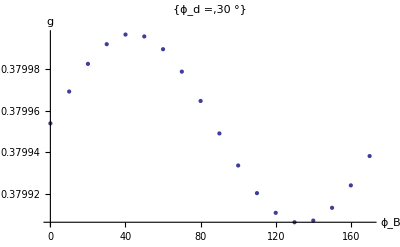
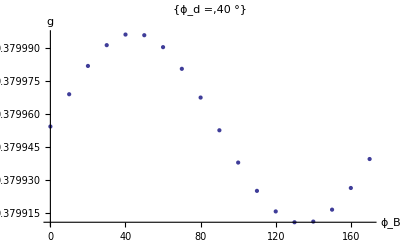
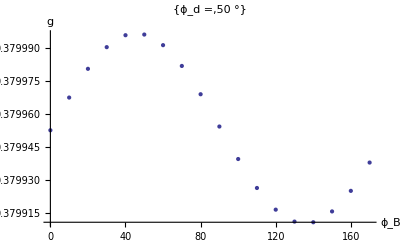
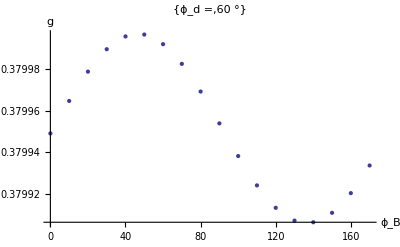
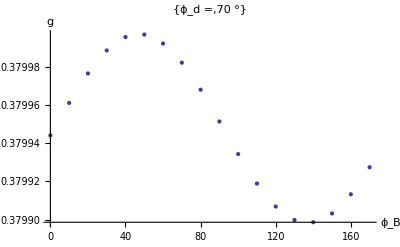

```mathematica
Table[ListPlot[Table[{gfactor[[i]][[1]],gfactor[[i]][[5]]},{i,1+18*j,18+18*j}],AxesLabel->{"ϕ_B","g"},PlotLabel->{"ϕ_d =",j*10 "°"}],{j,0,17}]
```

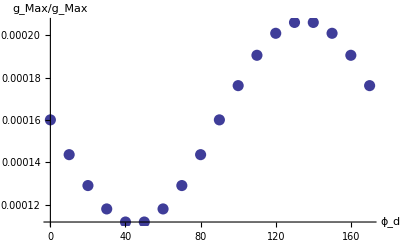

```mathematica
ListPlot[Table[{j*10,(Max[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]]-Min[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]])/(Max[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]]+Min[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]])},{j,0,17}],AxesLabel->{"ϕ_d","g_Max/g_Max"},PlotStyle->Directive[PointSize->0.02]]
```